```mathematica
(* note *)
```

```mathematica
ClearAll[LoadEigenEnergies,LoadAndBucketEnergies,PlotEnergyBuckets];
DataFolder = NotebookDirectory[]<>"../data/";
Format[energy,StandardForm]="E";

Options[LoadEigenEnergies]={Folder->DataFolder,Bucketed->False};
LoadEigenEnergies[s_,M_,opts:OptionsPattern[]]:=Module[{file,data},
file = "EEs="<> ToString[s] <> "M="<>ToString[M];
If[OptionValue[Bucketed], file = file <>"g"];
data = Import[OptionValue[Folder]<> file <> ".txt", "Table"];
If[OptionValue[Bucketed]==False, data=Flatten[data]];
Return[data];
];

LoadAndBucketEnergies[s_,M_,n_]:=Module[{data,maxE,delta, buckets,i,pos},
data=LoadEigenEnergies[s,M];
maxE=N[4*s*Cot[Pi/(2M)]];
delta=2*maxE/n;
buckets=ConstantArray[0,n];
pos=Floor[(data+maxE)/delta] + 1;
For[i=1,i≤Length[pos],i++,
buckets[[pos[[i]]]]=buckets[[pos[[i]]]]+1;
];

Return[{Table[Chop[-maxE+delta*(i-0.5)],{i,1,n}],buckets}]
];

PlotEnergyBuckets[s_,M_,n_]:=Module[{data,i,list},
data=LoadAndBucketEnergies[s,M,n];
list=Table[{data[[1,i]],data[[2,i]]},{i,1,Length[data[[1]]]}];
(*Print[list];*)
ListPlot[list]
];

PlotEnergyBuckets[s_,M_]:=Module[{data,tot,ndata,fit,p1,p2,p3,delta,i},
data=LoadEigenEnergies[s,M,Bucketed->True];
tot=Sum[data[[i,2]],{i,1,Length[data]}];
delta=data[[2,1]]-data[[1,1]];
ndata=Table[{data[[i,1]],data[[i,2]]/(tot*delta)},{i,1,Length[data]}];
fit=FitEnergyData[ndata];
p1=ListPlot[ndata];
p2=Plot[fit[x],{x, -N[4*s*Cot[Pi/(2M)]],N[4*s*Cot[Pi/(2M)]]}];
Show[p1,p2]
];

FitEnergyData[ndata_]:=Module[{lmf},
lmf=NonlinearModelFit[ndata[[5;;Length[ndata]-5]], 
1/Sqrt[2*Pi*sigma^2]Exp[-(x-mu)^2/(2*sigma^2)],
{mu, sigma}, {x}];
Return[lmf]
];

FitEnergyData[s_, M_]:=Module[{data, lmf, tot,ndata,delta},
data=LoadEigenEnergies[s,M,Bucketed->True];
tot=Sum[data[[i,2]],{i,1,Length[data]}];
delta=data[[2,1]]-data[[1,1]];
ndata=Table[{data[[i,1]],data[[i,2]]/(tot*delta)},{i,1,Length[data]}];
lmf=FitEnergyData[ndata];
Return[{mu,sigma}/.lmf["BestFitParameters"]];
];
```

{{19,3.40773,13.5941},{20,3.42988,13.9151},{21,3.43427,14.1918},{22,3.43657,14.4681},{23,3.43993,14.7429},{24,3.44837,15.0185},{25,3.45235,15.2834},{26,3.45492,15.5443}}

2.98018+0.0351869 x-0.000652746 x^2

{a→0.276765,b→8.36756}

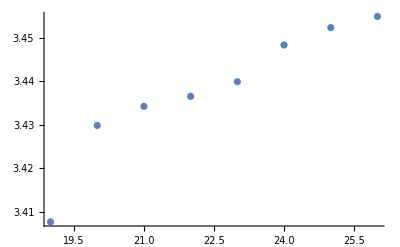

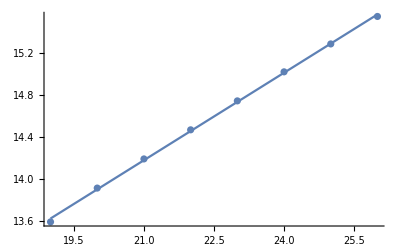

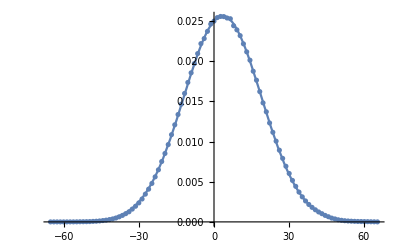

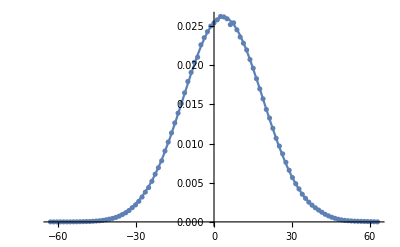

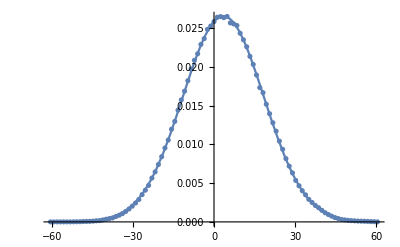

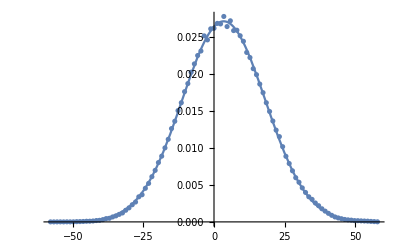

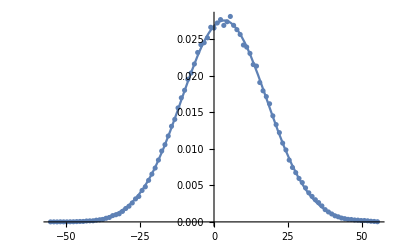

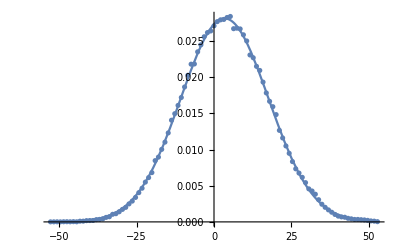

```mathematica
param=Table[Join[{m},FitEnergyData[1,m]],{m,19,26}]
param1=param[[All,{1,2}]];
param2=param[[All,{1,3}]];
tfit1=NonlinearModelFit[param1, a*x^2+b*x+c,{a, b,c}, {x}]//Normal
tfit2=NonlinearModelFit[param2, a*x+b,{a, b}, {x}];
tplot2=Plot[tfit2[x],{x,19,26}];
tfit2["BestFitParameters"]

ListPlot[param[[All,{1,2}]]]
Show[ListPlot[param[[All,{1,3}]]],tplot2]
PlotEnergyBuckets[1,26]
PlotEnergyBuckets[1,25]
PlotEnergyBuckets[1,24]
PlotEnergyBuckets[1,23]
PlotEnergyBuckets[1,22]
PlotEnergyBuckets[1,21]
PlotEnergyBuckets[1,20]
PlotEnergyBuckets[1,19]
```